# Hydrogen Atom Wave-function & Probability Density

## 1. Introduction

In this notebook, it was included the illustration for hydrogen atom wave-function and probability density. As is known, the hydrogen atom wave-function can be separated to radius part and angle part. The arizmuth angle part of the wave-function basically only concerns about the rotation around z-axis, when the wave-function is expressed in its complex form (physical, as compared to the real form of expression, which is chemical). For better understanding the ‘rotation effect’, the polar angle part of the wave-function was given in both 2D (where the arizmuth angle was fixed) and 3D (arizmuth angle from 0 to 2π). Also the animation showing the changing of the wave-function with both polar (for 2D plot) and arizmuth (for 3D plot) angle was given.

## 2. Define the Hydrogen Atom Wave-Function

The radius part of the wave-function contains the Laguerre polynomial and the exponential part. As for the angular part, the built-in spherical harmonics function in Mathematica was used. However, the spherical harmonics function in Mathematica contains the arizmuth angle by default. The arizmuch angle part was removed from the spherical harmonics function to get the polar angle part of the hydrogen wave-function.

```mathematica
Rnl[n_,l_,r_]:=(r^l)*Exp[-r/2]*LaguerreL[n-l-1,2*l+1,r];
```

```mathematica
Tlm[l_,m_,θ_] :=SphericalHarmonicY[l,m,θ,Pi]*Exp[-m I Pi]*Sqrt[2π];
```

### 2.0 The Notation

n 	- 	Principle quantum number
	l	- 	Angular momentum quantum number
	m	-	Magnetic quantum number

## 3. Angular Part of the Hydrogen Wave-Function

### 3.0 Important Note

The Mathematica built-in function was used to plot the angular part of the wave-function. For the plotting, the angular part of the wave-function was taken as the radius. When the evaluated wave-function value is negative, Mathematica will take its absolute value as the radius and add the angle value by π, which will make the new plot coincides with the positive part plotting. Therefore to explicitly show the negative part of the angular wave-function, the absolute value was taken as the radius argument. To see the difference between these two cases, refer to the animation below.

```mathematica
color[θ_]:=RGBColor[-Sign[Tlm[1,0,θ]],0,Sign[Tlm[1,0,θ]]];
```

```mathematica
Subscript[Θ,10]
```

Θ_10

```mathematica
Manipulate[Grid[{{PolarPlot[Abs[Tlm[1,0,Pi/2-θ]],{θ,0,theta},ImageSize->Scaled[0.2],PlotRange->{{-0.65,0.65},{-1.32,1.32}},Ticks->None,PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Absolute Value As Radius",FontColor->Magenta,FontSize->20],Epilog->{Arrow[{{0,1.38},{0,1.39}}],Arrow[{{0.68,0},{0.69,0}}],Text[Style["z",FontSize->18,Bold],{-0.05,1.35}],Text[Style["x",FontSize->18,Bold],{0.63,-0.05}],If[Tlm[1,0,Pi/2-theta]>0,{If[theta>0.5,Text[Style["+",FontSize->50,FontColor->Blue],Scaled[{0.50035,0.73}]]]},{Text[Style["+",FontSize->50,FontColor->Blue],Scaled[{0.50035,0.73}]],Text[Style["-",FontSize->50,FontColor->Red],Scaled[{0.50035,0.28}]]}]}],PolarPlot[Tlm[1,0,Pi/2-θ],{θ,0,theta},PlotRange->{{-0.65,0.65},{-1.32,1.32}},ImageSize->Scaled[0.2],Ticks->None,PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Original Value As Radius",FontColor->Magenta,FontSize->20],Epilog->{Text[Style["Two ways of plotting Θ_10 function",FontSize->18],{0,-0.5},Background->Yellow],Arrow[{{0,1.38},{0,1.39}}],Arrow[{{0.68,0},{0.69,0}}],Text[Style["z",FontSize->18,Bold],{-0.05,1.35}],Text[Style["x",FontSize->18,Bold],{0.63,-0.05}],If[Tlm[1,0,Pi/2-theta]>0,{If[theta>0.5,Text[Style["+",FontSize->50,FontColor->Blue],Scaled[{0.50035,0.74}]]]},{Text[Style["+",FontSize->50,FontColor->Blue],Scaled[{0.50035,0.74}]],Text[Style["-",FontSize->50,FontColor->Red],Scaled[{0.50035,0.72}]]}]}]}}],{{theta,0.0000001,"Polar Angle"},0.0000001,2Pi-0.0000001,AnimationRate->.5}]
```

### 3.1 Polar Angle Wave-Function Plotting - 2D (within x-z plane)

The polar angle part of the hydrogen atom wave-function is plotted in this part. The blue-colored line represents the positive value given by the polar angle wave-function (corresponds to the polar angle) and red-color corresponds to negative value. The polar angle starts from the positive x-axis and rotates in the counterclockwise direction.

#### Θ_00(θ)

```mathematica
color00[θ_]:=RGBColor[-Sign[Tlm[0,0,θ]],0,Sign[Tlm[0,0,θ]]];
```

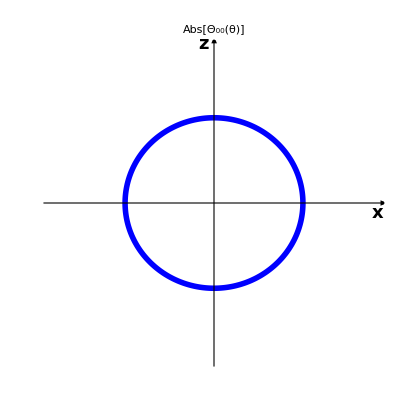

```mathematica
PolarPlot[Abs[Tlm[0,0,Pi/2-θ]],{θ,0,2Pi},Ticks->None,PlotRange->{{-1.3,1.3},{-1.3,1.3}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color00[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_00(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.32}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.37},{0.001,1.38}}],Arrow[{{1.37,0},{1.38,0}}]}]
```

#### Θ_10(θ) & Θ_(1,±1)(θ)

```mathematica
color10[θ_]:=RGBColor[-Sign[Tlm[1,0,θ]],0,Sign[Tlm[1,0,θ]]];
```

```mathematica
color11[θ_]:=RGBColor[-Sign[Tlm[1,1,θ]],0,Sign[Tlm[1,1,θ]]];
```

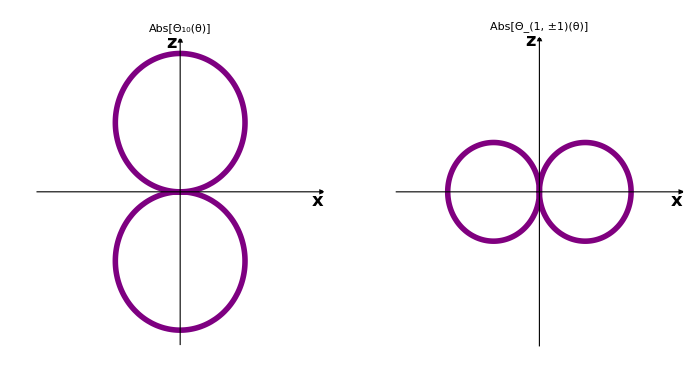

```mathematica
GraphicsRow[{PolarPlot[Abs[Tlm[1,0,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-1.3,1.3}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color10[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_10(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.32}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.37},{0.001,1.38}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[1,1,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-1.3,1.3}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color11[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(1, ±1)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.32}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.37},{0.001,1.38}}],Arrow[{{1.37,0},{1.38,0}}]}]}]
```

Here it should be pointed out that Mathematica gives a negative sign before the spherical harmonics for the case where l is odd number, e.g. Y_1^1(θ,ϕ)=-1/2 √(3/(2 π)) ⅇ^(ⅈ ϕ) sin(θ). Therefore the corresponding graphs showing the sign of the polar angle wave-function may be different from other sources. Anyways, it doesn’t matter that much since it is only the abolute value (actually, the square value) that matters.

#### Θ_20(θ) & Θ_(2,±1)(θ) & Θ_(2,±2)(θ)

```mathematica
color20[θ_]:=RGBColor[-Sign[Tlm[2,0,θ]],0,Sign[Tlm[2,0,θ]]];
```

```mathematica
color21[θ_]:=RGBColor[-Sign[Tlm[2,1,θ]],0,Sign[Tlm[2,1,θ]]];
```

```mathematica
color22[θ_]:=RGBColor[-Sign[Tlm[2,2,θ]],0,Sign[Tlm[2,2,θ]]];
```

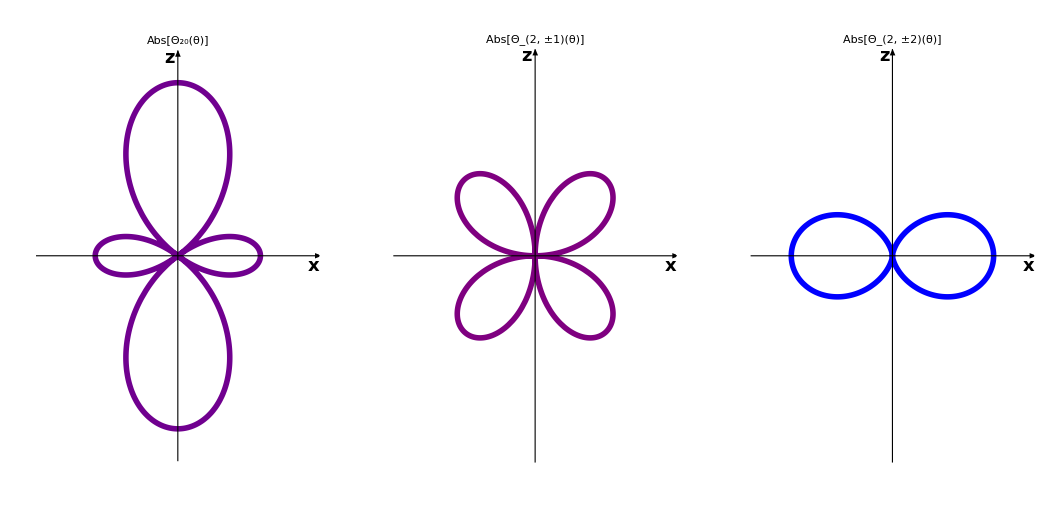

```mathematica
GraphicsRow[{PolarPlot[Abs[Tlm[2,0,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color20[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_20(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.82}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.87},{0.001,1.88}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[2,1,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color21[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(2, ±1)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.82}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.87},{0.001,1.88}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[2,2,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color22[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(2, ±2)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,1.82}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,1.87},{0.001,1.88}}],Arrow[{{1.37,0},{1.38,0}}]}]}]
```

#### Θ_30(θ) & Θ_(3,±1)(θ) & Θ_(3,±2)(θ) & Θ_(3,±3)(θ)

```mathematica
color30[θ_]:=RGBColor[-Sign[Tlm[3,0,θ]],0,Sign[Tlm[3,0,θ]]];
```

```mathematica
color31[θ_]:=RGBColor[-Sign[Tlm[3,1,θ]],0,Sign[Tlm[3,1,θ]]];
```

```mathematica
color32[θ_]:=RGBColor[-Sign[Tlm[3,2,θ]],0,Sign[Tlm[3,2,θ]]];
```

```mathematica
color33[θ_]:=RGBColor[-Sign[Tlm[3,3,θ]],0,Sign[Tlm[3,3,θ]]];
```

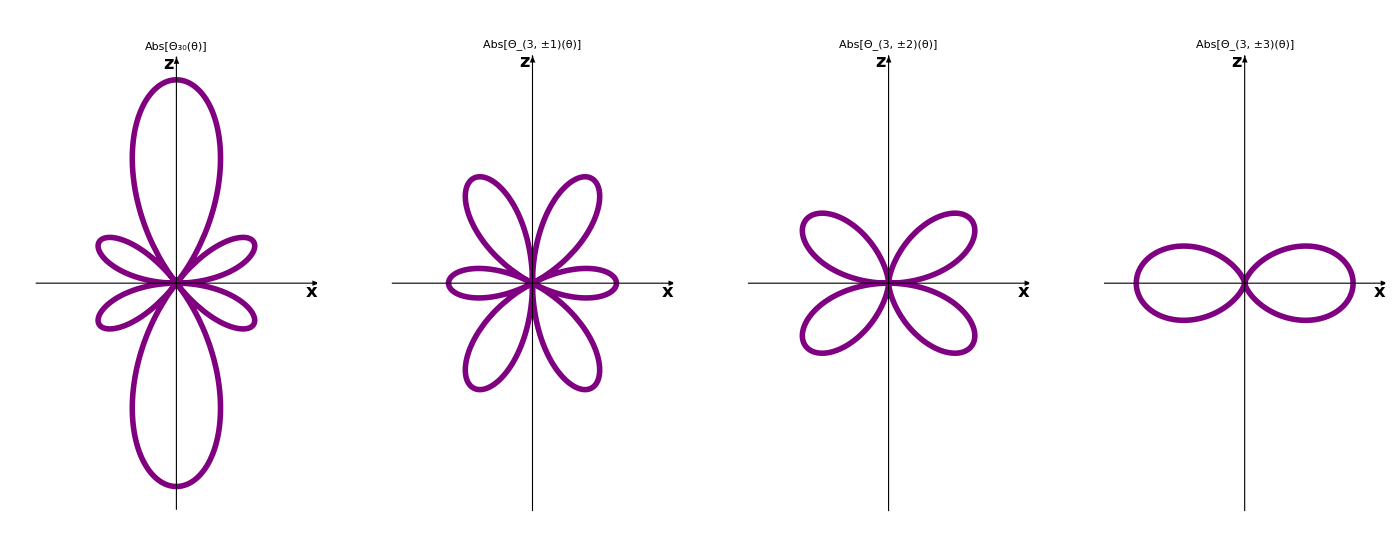

```mathematica
GraphicsRow[{PolarPlot[Abs[Tlm[3,0,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-2.0,2.0}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color30[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_30(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,2.02}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,2.07},{0.001,2.08}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[3,1,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-2.0,2.0}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color31[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(3, ±1)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,2.02}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,2.07},{0.001,2.08}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[3,2,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-2.0,2.0}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color32[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(3, ±2)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,2.02}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,2.07},{0.001,2.08}}],Arrow[{{1.37,0},{1.38,0}}]}],PolarPlot[Abs[Tlm[3,3,Pi/2-θ]],{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.7],PlotRange->{{-1.3,1.3},{-2.0,2.0}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color33[Pi/2-θ]],ColorFunctionScaling->False,PlotLabel->Style["Abs[Θ_(3, ±3)(θ)]",FontColor->Magenta,FontSize->20],Epilog->{ Text[Style["z",FontSize->18,Bold],{-0.08,2.02}],Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{0.001,2.07},{0.001,2.08}}],Arrow[{{1.37,0},{1.38,0}}]}]}]
```

### 3.2 Angular Distribution Probability Plotting (Square of Spherical Harmonics) - 3D

In this part, the 3D angular distribution probability function of the hydrogen atom is given. Basically, the complete angular part of the wave-function is the multiplication of polar angle part function Θ(θ) and arizmuth part function Φ(ϕ), which then makes the spherical harmonics given as: Y_l^m(θ,ϕ)=Θ_lm(θ)Φ_m(ϕ). When calculating the probability density, taking the square of the spherical harmonics will give a constant for the arizmuth part function. Therefore basically the distribution probability of hydrogen atom has nothing to do with the arizmuch angle ϕ. And the 3D plot can be simply thought as formed by rotating the above 2D polar plot around the z-axis.

#### |Θ_00(θ)|^2

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(Tlm[0,0,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_00(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-1,1},{-1,1},{-1,1}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,0.9}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.1,-0.1,0.8}]}]]}]
```

-Graphics-

#### |Θ_10(θ)|^2 & |Θ_(1,±1)(θ)|^2

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(Tlm[1,0,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_10(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-2,2},{-2,2},{-2,2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,1.9}]}]],Show[SphericalPlot3D[(Tlm[1,1,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(1, ±1)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-2,2},{-2,2},{-2,2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,1.3}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,1.2}]}]]}]
```

-Graphics-

#### |Θ_20(θ)|^2 & |Θ_(2,±1)(θ)|^2 & |Θ_(2,±2)(θ)|^2

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(Tlm[2,0,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_20(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-3.2,3.2},{-3.2,3.2},{-3.2,3.2}}],Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,3.2}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.3,-0.3,3.0}]}]],Show[SphericalPlot3D[(Tlm[2,1,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(2, ±1)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-3.2,3.2},{-3.2,3.2},{-3.2,3.2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,1.8}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.3,-0.3,1.7}]}]],Show[SphericalPlot3D[(Tlm[2,2,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[1],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(2, ±2)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-3.2,3.2},{-3.2,3.2},{-3.2,3.2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,1.8}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.3,-0.3,1.7}]}]]}]
```

-Graphics-

#### |Θ_30(θ)|^2 & |Θ_(3,±1)(θ)|^2 & |Θ_(3,±2)(θ)|^2 & |Θ_(3,±3)(θ)|^2

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(Tlm[3,0,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.8],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_30(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-4.5,4.5},{-4.5,4.5},{-4.5,4.5}}],Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,4.4}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,4.3}]}]],Show[SphericalPlot3D[(Tlm[3,1,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.8],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(3, ±1)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-4.5,4.5},{-4.5,4.5},{-4.5,4.5}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,3.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,2.9}]}]],Show[SphericalPlot3D[(Tlm[3,2,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.8],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(3, ±2)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-4.5,4.5},{-4.5,4.5},{-4.5,4.5}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,1.9}]}]],Show[SphericalPlot3D[(Tlm[3,3,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.8],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_(3, ±3)(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-4.5,4.5},{-4.5,4.5},{-4.5,4.5}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,1.6}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,1.5}]}]]}]
```

-Graphics-

#### The Illustration for Aangular Momentum Projection on z-axis

```mathematica
Magnetic`QN`Y10=Manipulate[Show[SphericalPlot3D[(Tlm[1,0,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.3],ViewPoint->{0,-2,0.3},PlotLabel->Style["|Θ_10(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-2,2},{-2,2},{-2,2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,1.9}]}],ParametricPlot3D[{(Tlm[1,0,θ])^2*Sin[θ]*Cos[phi],(Tlm[1,0,θ])^2*Sin[θ]*Sin[phi],(Tlm[1,0,θ])^2*Cos[θ]},{θ,0,2Pi},PlotStyle->Directive[Thick,Blue]],Graphics3D[{Blue,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{Sqrt[2]*Cos[Pi/2+phi],Sqrt[2]*Sin[Pi/2+phi],0}},0.02]]}]],{phi,0,2Pi,0.01,AnimationRate->30}]
```

```mathematica
Magnetic`QN`Y11=Manipulate[Show[SphericalPlot3D[(Tlm[1,1,θ])^2,{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->None,ImageSize->Scaled[0.6],ViewPoint->{1,1,1},PlotLabel->Style["|Θ_11(θ)|^2",FontColor->Magenta,FontSize->20],PlotRange->{{-2,2},{-2,2},{-2,2}}],ParametricPlot3D[{(Tlm[1,1,θ])^2*Sin[θ]*Cos[phi+ArcSin[Cot[θ]]],(Tlm[1,1,θ])^2*Sin[θ]*Sin[phi+ArcSin[Cot[θ]]],(Tlm[1,1,θ])^2*Cos[θ]},{θ,0,2Pi},PlotStyle->Directive[Thick,Blue]],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.6,1.9}]}],Graphics3D[{Blue,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{Sin[phi],-Cos[phi],1}},0.02]]}]],{phi,0,2Pi,0.01,AnimationRate->30}]
```